```mathematica
ClearAll[r, x, y, z];
r0 = 1;
r[θ_, r0_] := r0 Sin[θ]^2;
x[θ_, φ_, r0_] := r[θ, r0] Sin[θ] Cos[φ];
y[θ_,  φ_, r0_] := r[θ, r0] Sin[θ] Sin[φ];
z[θ_,  φ_, r0_] := r[θ, r0] Cos[θ];
```

```mathematica
φ = π/4;
r0 = 1/4;
img = ParametricPlot3D[{
x[θ, φ, r0], y[θ, φ, r0], z[θ, φ, r0]
}, {θ, 0, 2π}, {φ, 0, 2π} ,
 PlotStyle->{Opacity[0.5], RGBColor[0, 0.7, 0]}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
path = "D:\\Kami\\git_folder\\notes_4sem\\field_theory\\homework\\figures\\"
Export[path<>"T13.pdf", img]
```

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\T13.pdf

## ТеорВер

### Четвертая задача

```mathematica
f = c Exp[-y^2+4 y - 10];
F = Integrate[f, {y, -∞, +∞}]
```

(c √π)/ⅇ^6

```mathematica
Solve[F == 1, c]⟦1⟧
```

{c→ⅇ^6/(√π)}

```mathematica
-y^2+4 y - 10 
y^2-4 y + 10 
Expand[-(y-2)^2-6]
```

-10+4 y-y^2

10-4 y+y^2

-10+4 y-y^2

```mathematica
f2 = ⅇ^6/(√π)Exp[-y^2+4 y - 10];
Integrate[f2, y]
Integrate[y f2, y]
Integrate[y^2 f2, y]
Integrate[f2, {y, -∞, +∞}]
Integrate[y f2, {y, -∞, +∞}]
Integrate[y^2 f2, {y, -∞, +∞}]
```

-1/2 Erf[2-y]

(-1/2 ⅇ^(-(-2+y)^2)-√π Erf[2-y])/(√π)

-(ⅇ^(-(-2+y)^2) (4+2 y+9 ⅇ^((-2+y)^2) √π Erf[2-y]))/(4 √π)

1

2

9/2

### Вторая задача

```mathematica
M2=({{Cov[X, X], Cov[X, Y], Cov[X, Z]}, {Cov[Y, X], Cov[Y, Y], Cov[Y, Z]}, {Cov[Z, X], Cov[Z, Y], Cov[Z, Z]}});
```

```mathematica
Λ[β_]:=({{γ, -β γ, 0, 0}, {-β γ, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
Λ[-β].{γ Subscript[ω, 0],γ Subscript[ω, 0] Cos[θ'], γ Subscript[ω, 0] Sin[θ'], 0}  // FullSimplify // MatrixForm
```

(γ^2 (1+β Cos[θ']) ω_0
γ^2 (β+Cos[θ']) ω_0
γ Sin[θ'] ω_0
0)

```mathematica
0.06/(√(0.42 0.58))
```

0.121566

```mathematica
Не
```

```mathematica
Erf[1.96]
```

0.994426

```mathematica
n = 260;
a = 0.36n;
b= 0.48 n;
σ = √(n 0.42 0.58);
e = n  0.42;
ClearAll[σ, e, a, b, n];
Integrate[1/(√(2π)σ)Exp[-(x-e)^2/(2 σ^2)]
, {x, a, b}]
```

1/2 (Erf[(-a+e)/(√2 σ)]-Erf[(-b+e)/(√2 σ)])

```mathematica
-1/2 Erf[(a-b)/(√2 σ)] /. {a-> 0.36, b -> 0.48}
```

1/2 Erf[0.0848528/σ]

```mathematica
(*n = 260;*)
a = 0.36n;
b= 0.48 n;
σ = √(n 0.42 0.58);
e = n  0.42;
(-a+e)/(√2 σ)
```

0.0859602 √n

```mathematica
Erf[]
```

0.950027

```mathematica
0.085960238 √260
```

1.38607

```mathematica
M = ({{2, -1, λ}, {-1, 2, 1}, {λ, 1, 3}});
```

```mathematica
Det[M]
```

7-2 λ-2 λ^2

```mathematica
Solve[Det[M]==0, λ]
```

```mathematica
{{λ->1/2 (-1-√15)},{λ->1/2 (-1+√15)}}
```

```mathematica
ξ = {1, λ, -2};
Solve[D[FullSimplify[ξ.M.ξ], λ] == 0, λ]
```

{{λ→5/2}}

```mathematica
Expand@FullSimplify[ξ.M.ξ]
```

14-10 λ+2 λ^2

```mathematica
N[(-1 + √15)/2]
```

1.43649

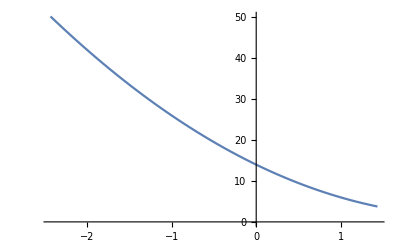

```mathematica
c1 = N[1/2 (-1-√15)];
c2 = N[1/2 (-1+√15)];
Plot[14-10 λ+2 λ^2, {λ, c1, c2}]
```

```mathematica
Sum[KroneckerDelta[i,j], {i, 61, 100}, {j, 1, 80}]
```

```mathematica
N@Log2[20/(√(40 80))]
ρ = 20/(√(40 80))
```

-1.5

1/(2 √2)

```mathematica
FullSimplify[√(40 80)√(1-ρ^2)]
```

20 √7

```mathematica
1/(2(1-ρ^2))
```

4/7

```mathematica
(2ρ)/(√(40 80))
```

1/80

```mathematica
s = "\\frac{1}{\\sqrt{2\\pi}^2 \\sigma_1 \\sigma_2 \\sqrt{1-\\rho^2}} \\exp\\left(
            - \\frac{1}{2(1-\\rho^2)} \\left[
                \\frac{(x_1-a_1)^2}{\\sigma_1^2} - \\rho \\frac{2 (x_1 - a_1)(x_2-a_2)}{\\sigma_1 \\sigma_2} + \\frac{(x_2-a_2)^2}{\\sigma_2^2}
            \\right]
        \\right)";
```

```mathematica
ClearAll[σ, x1, x2];
a1 = 0;
a2 = 0;
σ1 = √40 σ;
σ2 = √80 σ;
ρ = (20 σ^2)/(σ1 σ2);
```

```mathematica
FullSimplify[1/(2 π σ1 σ2 √(1-ρ^2)), σ>0]
```

1/(40 √7 π σ^2)

```mathematica
FullSimplify[-1/(2(1-ρ^2))((Y-a1)^2/σ1^2- ρ 2/(σ1 σ2)Y Z + Z^2/σ2^2)
, σ>0]
```

-(2 Y^2-Y Z+Z^2)/(140 σ^2)

```mathematica
e = 4.8 10^-10;
a = 10^-8 ;
r0 = 10^-13;
ScientificForm[e^2/a]
```

2.304×10^-11

```mathematica
ScientificForm[4./9(1/2) (r0/a)^2]
```

2.22222×10^-11

```mathematica
0.009 3 10^5
```

2700.

## Механика

```mathematica
ClearAll[m, x, y, q, Q, z, r];
X = x[t];
Y= y[t];
v2 =
```

```mathematica
H = m
```

```mathematica
2+2
```

4

```mathematica
P = p[t]; Q=q[t];
eqs = {D[Q, t]-P - 2 λ (P^2/2+(ω^2 Q^2)/2)P== 0,
D[P, t] + Q + 2 λ (Q^2/2+(ω^2 Q^2)/2)ω^2 Q== 0};
Assuming[λ>0&&ω>0, DSolve[{
D[x[t],t]== y[t] x[t] λ (1-ω^2),
D[y[t], t] == x[t] (ω^2-1)
}, {x[t], y[t]}, t]] // FullSimplify
```

{{y[t]→-√2 √(C[1] Tanh[1/2 √λ √C[1] (√2 t √λ (-1+ω^2)+C[2])]^2),x[t]→λ C[1] Sech[1/2 √λ √C[1] (√2 t √λ (-1+ω^2)+C[2])]^2},{y[t]→√2 √(C[1] Tanh[1/2 √λ √C[1] (-√2 t √λ (-1+ω^2)+C[2])]^2),x[t]→λ C[1] Sech[1/2 √λ √C[1] (-√2 t √λ (-1+ω^2)+C[2])]^2}}

```mathematica
y1 = 4 C[1]^2 Tanh[ C[1]( γ t  +C[2])];
x1 =  4 C[1]^2 Sech[C[1] (γ t+C[2])]^2;
```

```mathematica
FullSimplify[{x1, y1} // TrigToExp]
```

```mathematica
{,}
```

```mathematica
γ = √(2λ)(-1+ω^2) ;
x = 4 C[1]^2 Sech[C[1] (t γ+C[2])]^2;
y = 4 C[1]^2 Tanh[C[1] (t γ+C[2])];
```

```mathematica
FullSimplify[Solve[{x== p q, y == q^2 ω^2+p^2}, {p, q}] , λ>0&&ω>0]
```

{{p→-((2 √2 ω C[1]^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)/(√(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]-√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2))))),q→-1/ω(√(2 C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]-2 √(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2))))},{p→(2 √2 ω C[1]^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)/(√(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]-√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)))),q→1/ω(√(2 C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]-2 √(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2))))},{p→(2 √2 ω C[1]^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)/(√(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]+√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)))),q→1/ω √2 √(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]+√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)))},{p→-((2 √2 ω C[1]^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)/(√(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]+√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2))))),q→-1/ω √2 √(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]+√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)))}}

```mathematica
eq = -((2 √2 ω C[1]^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)/(√(C[1]^2 Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]-√(C[1]^4 (-4 ω^2 Sech[C[1] (√2 t √λ (-1+ω^2)+C[2])]^4+Tanh[C[1] (√2 t √λ (-1+ω^2)+C[2])]^2)))));
eq /. {C[1] (√2 t √λ (-1+ω^2)+C[2] )-> T}
```

```mathematica
eq2 = -(2 √2 ω C[1] Sech[T]^2)/(√(Tanh[T]-√(-4 ω^2 Sech[T]^4+Tanh[T]^2)));
```

```mathematica
eq3 = (eq2 // TrigToExp) /. {ⅇ^-T+ⅇ^T -> G1,- ⅇ^-T+ⅇ^T-> G2}
```

-(8 √2 ω C[1])/(G1^2 √(G2/G1-√(G2^2/G1^2-(64 ω^2)/G1^4)))

```mathematica
FullSimplify[eq3]
```

```mathematica
-(8 √2 ω C[1])/(ⅇ^-T+ⅇ^T √(2 Sinh[2 T]-√(4 Sinh[2 T]^2-64 ω^2))) // FullSimplify // ExpToTrig // FullSimplify
```

-(8 √2 ⅇ^T ω C[1])/(1+ⅇ^(2 T) √(-√(-2-64 ω^2+2 Cosh[4 T])+2 Sinh[2 T]))

```mathematica
(ⅇ^-T+ⅇ^T )(- ⅇ^-T+ⅇ^T) // FullSimplify
```

2 Sinh[2 T]

```mathematica
d = (A + ⅈ B) Exp[- ⅈ ω t]+(A - ⅈ B) Exp[ ⅈ ω t];
```

```mathematica
TrigExpand@FullSimplify[d^2/2]
```

A^2+B^2+A^2 Cos[t ω]^2-B^2 Cos[t ω]^2+4 A B Cos[t ω] Sin[t ω]-A^2 Sin[t ω]^2+B^2 Sin[t ω]^2

```mathematica
Integrate[d^2, {t,0, (2 π)/ω}]/(2 π/ω)
```

2 (A^2+B^2)

```mathematica
ρ = r/a Cos[θ] Exp[-3/2 r/a];
```

```mathematica
f = ρ r r^2 Sin[θ] Cos[θ]
```

(ⅇ^(-(3 r)/(2 a)) r^4 Cos[θ]^2 Sin[θ])/a

```mathematica
Integrate[f, {θ, 0, π}, {φ, 0, 2π}, {r, 0, ∞}]
```

(1024 a^4 π)/243

```mathematica
2^10
```

1024

```mathematica
3^5
```

243

```mathematica
Integrate[Cos[θ]^2 Sin[θ], θ]
```

-1/3 Cos[θ]^3

## подставь

```mathematica
(* A = 2^9, B = 3^5, N[2^9/3^5] = 2.107*)
 a = ℏ/(m c α); d = (e a)/(√2)2.107; J =ω^4 4/(3 c^3)d^2;
```

```mathematica
τ = ((ℏ ω)/J) /. {1/e^2-> 1/(ℏ c α)}
```

(0.33788 c^4 m^2 α)/(ω^3 ℏ^2)

```mathematica
(τ /. {1/ω^3-> (ℏ/(3/8 c^2 m α^2))^3}) /. {m c^2 -> 0.5}
```

(6.4072 ℏ)/(c^2 m α^5)

```mathematica
(6.4072 (4.136 10^-15))/(0.5 10^6)137^5
```

2.55789×10^-9

```mathematica
eq2 /. {ℏ -> , 1/(m c^2)-> 1/0.5, 1/α^5-> 137^5}
```

(12.8144 ℏ)/α^5

```mathematica
(12.81440306868913 ℏ)/α^5
```

```mathematica
200/(3 10^10) // N
```

6.66667×10^-9

```mathematica
eq = FullSimplify[τ]
```

(0.33788 c^4 m^2 α)/(ω^3 ℏ^2)

```mathematica
m ->
```

```mathematica
F[n_] := -1/2 m c^2 α^2 1/n^2;
```

```mathematica
F[2]-F[1]
```

3/8 c^2 m α^2

```mathematica
ScientificForm[29979245800.00]
```

2.99792×10^10

```mathematica
3/8 3^11/2^19(1/137)^3(0.5)^3/200^3(3 10^10)^3
```

2.05316×10^-15

```mathematica
0.35/(3/8)^3 200/0.5 1/137^5 1/(3 10^10)
```

1.83362×10^-18

```mathematica
Integrate[(1+Cos[θ]^2)Sin[θ], {θ, 0, π}, {φ, 0, 2π}]
```

(16 π)/3

```mathematica
Manipulate[
x = A1 Cos[t];
y = A2 Sin[t+2π φ];
ListLinePlot[{{0,0},{x ,y}}, PlotRange->{{-2,2}, {-2, 2}}, PlotStyle->{Thick, Blue}, AspectRatio->1]
, {t, 0, 2π}, {A1, 1, 2}, {A2, 1, 2}, {φ, 0,1}]
```

## Даше

### Первый номер

```mathematica
ClearAll[F];
F[x_] := 1 /; EvenQ[x];
F[x_] := -1 /; OddQ[x];
F[x_] := 0 /; x ∈Reals;
```

```mathematica
F[7]
F[6]
F[7.5]
F[7ⅈ + 4]
```

-1

1

0

F[4+7 ⅈ]

### Второй номер

```mathematica
ClearAll[g, a, b, c, d, x, f, L, a1, a2, a3, a4];
L[x__] := Plus[x] /; DeleteDuplicates[{x}] == {x};
L[x__] := g[x];
eq = g[1, 2] +  a2 f[g[6, 7, 9]] + a3 g[1, 1, 1]+a4* g[4, 3, 2]
eq /. {g[x__] :>  L[x]}
```

a2 f[g[6,7,9]]+g[1,2]+a3 g[1,1,1]+a4 g[4,3,2]

3+9 a4+a2 f[22]+a3 g[1,1,1]

{3+9 a4+f[22]+a3 g[1,1,1],3+9 a4+2 f[22]+a3 g[1,1,1],3+9 a4+3 f[22]+a3 g[1,1,1]}

```mathematica
eq // FullForm
```

Plus[Times[a2,f[g[6,7,9]]],Times[a3,g[1,1,1]],g[1,2,4],Times[a4,g[4,3,2]]]

```mathematica
L[{1, 1, 1}]
```

3

```mathematica
a1 = {1, 2, 3, 3};
a2 = {1, 2, 3};
DeleteDuplicates[a1] == a1
DeleteDuplicates[a2] == a2
```

False

True